# Adding Edges to Biconnect a Graph

## Algorithm

The best known algorithm to biconnect a graph is given in [1]. Here an iterative approach is implemented:
1. On an event, variable network is updated and triggers a function.
2. The function:
2a. b = Find bicomponents of network
2b. b_sorted = sort bicomponents according to smallest total edge degree
2c. b2 = take two bicomponents from b_sorted
2d. b2_sorted = sort vertices in each bicomponent according to edge degree
2e. Remove vertices that exist in both bicomponents
2e. Select vertex a from the first component and vertex b from the second components with the smallest edge degree
2f. Return (a,b)
3. Create link  (a,b)

(The network is updated. Once the link is added, an event will be raised.)

The algorithm is complete when 1) no event triggers a network update, so the algorithm is not executed, or 2) when there is onle one bicomponent, the network is then biconnected.

## J/Link

Jlink is used to listen to Sarastro events. On each event, the Java code pulls the edges in the network from Sarastro.

```mathematica
Needs["JLink`"];
```

```mathematica
ReinstallJava[];
```

```mathematica
AddToClassPath["/Users/rudolf/Desktop/phd/code/current/vinet_working/mathconnector/dist/InteractiveNetworksMathematica.jar"];
```

```mathematica
ShowJavaConsole[]
```

«JavaObject[com.wolfram.jlink.ui.ConsoleWindow]»

```mathematica
user = "rstrijk@gmail.com"
vid=9;
client=LoadJavaClass["interactivenetworksmathematica.SarastroEventSource"]
myclient=JavaNew[client,"http://localhost:4567/netapp/feed?userid="<>user<>"&vid="<>ToString[vid], "http://localhost:4567/netapp/links?userid="<>user<>"&vid="<>ToString[vid]];
myclient@start[]
```

rstrijk@gmail.com

JavaClass[interactivenetworksmathematica.SarastroEventSource,<>]

```mathematica
myclient@stop[]
```

## Implementation

```mathematica
<<GraphUtilities`

user ="rstrijk@gmail.com"

CreateLinkMockup::usage:="CreateLink[e] calls the web inteface of the on-demand network to create a link."
CreateLinkMockup[e_]:=If[Length[e]==2,network =EdgeAdd[network,UndirectedEdge@@e];
Print["creating: "<>ToString[e]]; hist=Append[hist, network]]

CreateLinkReal::usage:="CreateLink[e] calls the web inteface of the on-demand network to create a link."
CreateLinkReal[e_]:=
If[Length[e]==2,Import["http://localhost:4567/netapp/link","Text","RequestMethod"->"POST","RequestParameters"->{"src"->e[[1]],"dst"->e[[2]], "vid"->ToString[vid],"userid"->user}];(*oldnet=Graph[{}];*)
Print["creating: "<>ToString[e]]; hist=Append[hist, network]]

(* XXX: why doesn't the ring work optimally anymore? something with vertexlist and vertex degree!! check dry*)
(* XXX: Problem: a resulting edge can already be part of the graph! should remove the edge and try further... *)
ConnectTwoComponents::usage:="ConnectTwoComponents[s] selects an edge to create from a set of biconnected components."
ConnectTwoComponents[s_,n_]:=Module[{edge,c,i,r,v=VertexDegree[n],vl=VertexList[n]},If[Length[s]<=1,Return[{}]];
If[Length[s]>1,
c=Take[s,2];
i=Intersection@@c;
If[Length[i]>0,r=Delete[c,Position[c,i[[1]]]],r=c]];
Map[First,Map[Sort[#,v[[Position[vl,#1][[1]]]][[1]]<v[[Position[vl,#2][[1]]]][[1]]&]&,r]]]

MyBicomponents::usage:="MyBicomponents[n] returns results of Bicomponents[n] sorted by edge degree."
MyBicomponents[n_]:=Module[{a,v=VertexDegree[n],vl=VertexList[n]},{Sort[Bicomponents[n],(Function[{x},Total[v[[Position[vl,#][[1]]]]&/@x]][#1][[1]])<(Function[{x},Total[v[[Position[vl,#][[1]]]]&/@x]][#2][[1]])&],n}]

ResolveArticulationVertices::usage:="ResolveArticulationVertices[n] iteratively adds edges to a network to resolve single points of failure."
ResolveArticulationVertices[n_]:=(If[!IsomorphicGraphQ[oldnet,network],( oldnet=network;CreateLinkReal[ConnectTwoComponents@@MyBicomponents[n]])]; network)

ResolveArticulationVerticesMockup::usage:="ResolveArticulationVertices[n] iteratively adds edges to a network to resolve single points of failure."
ResolveArticulationVerticesMockup[n_]:=If[!IsomorphicGraphQ[oldnet,network], (oldnet=network;CreateLinkMockup[ConnectTwoComponents@@MyBicomponents[n]])]

hist={};
oldnet=Graph[{}];
MyPlot[n_]:=GraphPlot[#,VertexLabeling->True,DirectedEdges->False]&/@(If[Last[hist]!=n,hist=Append[hist,n]];hist)
```

rstrijk@gmail.com

## Examples

Start the dynamics, such that an updated graph will trigger the function call and display the graph when the network changes.

```mathematica
Dynamic[MyPlot[ResolveArticulationVertices[network]]]
```

```mathematica
Dynamic[MyPlot[ResolveArticulationVertices[network]]]
```

## Examples 2

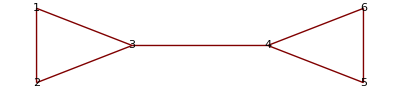

```mathematica
network=Graph[{1<->2,2<->3,3<->1,3<->4,4<->5,5<->6,4<->6}];
GraphPlot[network,VertexLabeling->True,DirectedEdges->False]
```

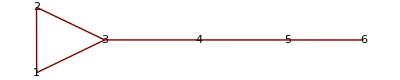

```mathematica
network=Graph[{1<->2,2<->3,3<->1,3<->4,4<->5,5<->6}];
GraphPlot[network,VertexLabeling->True,DirectedEdges->False]
```

Expected output:
"creating: {6, 4}"
"creating: {4, 1}"
"creating: {6, 1}"

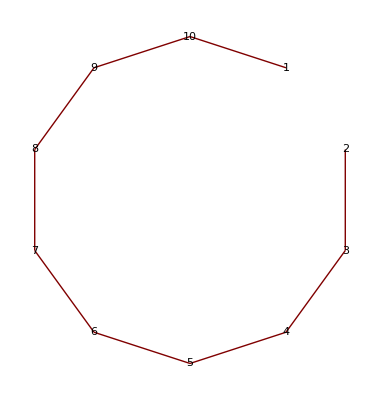

```mathematica
network=EdgeDelete[CycleGraph[10,DirectedEdges->False],1<->2];
GraphPlot[network,VertexLabeling->True,DirectedEdges->False]
```

Expected output:
"creating: {100, 2}"

## References

[1] Tsan-sheng Hsu, Vijaya Ramachandran, “On Finding a Smallest Augmentation to Biconnect a Graph, SIAM Journal on Computing”, 1993

```mathematica
network=testnetwork
```

-Graphics-

```mathematica
testnetwork=RandomGraph[DegreeGraphDistribution[RandomInteger[{1,3},30]]]
```

-Graphics-